```mathematica
Clear["Global`*"]
```

## All of the following is for a kappa dist(!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!)

```mathematica
phiBarK[phiBar_,kappa_]:=phiBar/(kappa-3/2)
```

```mathematica
Integrand[kappa_,t_]:=t^(kappa-3/2)(1-t)^(1/2)
```

```mathematica
Aich1[u1_,u2_,kappa_]:=NIntegrate[t^(kappa-3/2)(1-t)^(1/2),{t,u1,u2},WorkingPrecision->18]
```

Original

```mathematica
(*densFacK[phiBarK_,kappa_,RB_]:=1/2 Gamma[kappa+1]/(Gamma[3/2]Gamma[kappa-1/2])( (1-RB-phiBarK)^(1/2)(1+phiBarK/(RB-1))^-kappa Aich1[1/(1+RB)(1-RB/(1-phiBarK)),(1-RB-phiBarK)/((1+RB)(1+phiBarK/(RB-1))),kappa]+1/(1-phiBarK)^(kappa-1/2)Aich1[0,1-phiBarK,kappa]);*)
```

Try #2: replace first argument of Aich1 with something possibly simpler, which also matches the outside: 1/(1+RB)(1-RB/(1-phiBarK))-> (1-RB-phiBarK)/((1+RB)(1-phiBarK))

```mathematica
densFacK[phiBarK_,kappa_,RB_]:=1/2 Gamma[kappa+1]/(Gamma[3/2]Gamma[kappa-1/2])( (1-RB-phiBarK)^(1/2)(1+phiBarK/(RB-1))^-kappa Aich1[(1-RB-phiBarK)/((1+RB)(1-phiBarK)),(1-RB-phiBarK)/(1+RB+phiBarK),kappa]+1/(1-phiBarK)^(kappa-1/2)Aich1[0,1-phiBarK,kappa])
```

Still not working ...

#### Chunked-out parts of the densFacK function

```mathematica
part1[phiBarK_,kappa_,RB_]:=(1-RB-phiBarK)^(1/2)(1+phiBarK/(RB-1))^-kappa
part1Aich1[phiBarK_,kappa_,RB_]:=Aich1[1/(1+RB)(1-RB/(1-phiBarK)),(1-RB-phiBarK)/((1+RB)(1+phiBarK/(RB-1))),kappa]
```

```mathematica
part2[phiBarK_,kappa_,RB_]:=1/(1-phiBarK)^(kappa-1/2)
part2Aich1[phiBarK_,kappa_,RB_]:=Aich1[0,1-phiBarK,kappa]
```

```mathematica
p1H1Arg1[phiBarK_,RB_]:=1/(1+RB)(1-RB/(1-phiBarK))
p1H1Arg2[phiBarK_,RB_]:=(1-RB-phiBarK)/((1+RB)(1+phiBarK/(RB-1)))
```

```mathematica
p2H1Arg2[phiBarK_]:=1-phiBarK
```

```mathematica
kappa=5;
```

```mathematica
dPhi=941;T=110;
RB=10;
```

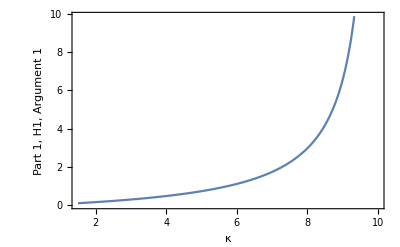

```mathematica
Plot[FullSimplify[p1H1Arg1[phiBarK[941/110,kappa],10]],{kappa,1.5,10},Frame->True,FrameLabel->{"κ","Part 1, H1, Argument 1"}]
```

```mathematica
Plot[FullSimplify[p1H1Arg2[phiBarK[941/110,kappa],10]],{kappa,1.5,10},Frame->True,FrameLabel->{"κ","Part 1, H1, Argument 2"}]
```

-Graphics-

```mathematica
Plot[Re[densFacK[phiBarK[dPhi/T,kappa],kappa,
```

```mathematica
densFacK[phiBarK[dPhi/T,kappa],kappa,3]
```

1.896063886636499-0.00930895551285442581 ⅈ

```mathematica
part1[phiBarK[dPhi/T,kappa],kappa,RB]
```

(4455 ⅈ √(55/359))/2872

```mathematica
part1Aich1[phiBarK[dPhi/T,kappa],kappa,RB]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-0.00162423377385046069}. NIntegrate obtained -0.0359919664301874989-0.60081752413889727 ⅈ and 5.53153461850159483×10^-7 for the integral and error estimates.

-0.0359919664301874989-0.60081752413889727 ⅈ

```mathematica
N[p1H1Arg1[phiBarK[dPhi/T,kappa],RB]]
```

0.147342

```mathematica
N[p1H1Arg2[phiBarK[dPhi/T,kappa],RB]]
```

-0.818182

```mathematica
part2[phiBarK[dPhi/T,kappa],kappa,RB]
```

55/886 ⅈ √(55/886)

```mathematica
phiBarK[dPhi/T,kappa]
```

28.5152